# Homework 14

## Non-rigid box and simple harmonic oscillator Steve Turley: Physics 222, Fall 2011

This homework assignment will give you some practice learning about the stationary states for a non-rigid box and a simple harmonic oscillator.

Some of you have asked for some more challenging homework problems.  Others of you are saying you're barely getting this material (or in some cases, not quite).  My solution is to add some bonus questions on the homework.  In general these are quite challenging and are ones for which I won't provide solutions or detailed help.  They are significantly beyond what will be expected on the exams or what I'd expect most of you to be able to do.

## Problem 1

In this problem, you will find the energy levels and wave functions for a particle in a square well potential.  The walls of the well are at the points where x=0 and x=a.  We will restrict ourselves to the case of bound states, where the total energy is greater than 0 (the potential at the bottom of the well) and U_0, the potential at the top of the well.  In this case, the wave function inside the box has a form of A sin(k x)+B cos(k x) and the potential outside the well has a form C e^-αx for x>a and D e^αx for x<0.  The exponential solutions have been chosen to be the ones which go to zero at -∞ and ∞, thus making the wave function normalizable.  The values A, B, C, and D are constants to be determined by the boundary conditions.

In this case, k is given by the relation E_1=(k^2 ℏ^2)/(2 m)  and alpha by the relation U_0-E_1=(α^2 ℏ^2)/(2 m).  Since the wave function needs to be continuous and have a continuous first derivative, your job is to find the particular solutions which match the boundary conditions of continuity at 0 and a.

### Example

I will gave you an example solution of how to find the ground state energy for a particular case where I've chosen U_0=5 eV, m=1MeV/c^2,  and a=1.5 nm.

First find the formulas for k and alpha.  We’ll begin by defining the constants for our potential and mass.

```mathematica
a=1.5;
U0=5;
mc2=1000000; (* mc^2 in units of eV *)
```

Note that in the following two expressions, you'll need to find your own functions for k and α with the correct masses, energies, and well width.

```mathematica
hbarc=1240/(2*Pi); (* units of eV-nm *)
k[e1_]:=Sqrt[2*mc2*e1/hbarc^2]
alpha[e1_]:=Sqrt[2*mc2*(U0-e1)/hbarc^2]
```

Now find the wave function inside the well for a given value of energy and position.

```mathematica
psi2[x_,e1_]:=A*Sin[k[e1]*x]+B*Cos[k[e1]*x]
```

psi1 will be the wave function for x<0.  I'll arbitrarily set its amplitude to 1, since everything will have to be normalized later.

```mathematica
psi1[x_,e1_]:=Exp[alpha[e1]*x]
```

psi3 will be the wave function for x>a

```mathematica
psi3[x_, e1_]:=C*Exp[-alpha[e1]*x]
```

There are four boundary conditions which need to be met.  This leaves me with four equations and four unknowns (A, B, C, and e1).

Set the boundary condition of continuity at x=0  and x=a

```mathematica
eq1=psi1[0,e1]==psi2[0,e1]
eq2=psi2[a,e1]==psi3[a,e1]
```

1==B

A sin(10.7489 √e1)+B cos(10.7489 √e1)==C ⅇ^(-10.7489 √(5-e1))

Set the boundary condition of continuity of psi'(x) at x=0 and x=a.  First I'll need functional forms for the derivatives, then I force the derivatives to their proper value.

```mathematica
psi1prime[x_,e1_]:=Evaluate[D[psi1[x,e1],x]]
psi2prime[x_,e1_]:=Evaluate[D[psi2[x,e1],x]]
psi3prime[x_,e1_] := Evaluate[D[psi3[x,e1],x]]
eq3=psi1prime[0,e1]==psi2prime[0,e1]
eq4=psi2prime[a,e1]==psi3prime[a,e1]
```

50/31 √2 π √(5-e1)==50/31 √2 π A √e1

50/31 √2 π A √e1 cos(10.7489 √e1)-50/31 √2 π B √e1 sin(10.7489 √e1)==-50/31 √2 π C ⅇ^(-10.7489 √(5-e1)) √(5-e1)

I can solve for three of these four equations for any arbitrary e1 since there will then be three equations and three unknowns.  The fourth equation only has solutions for special values of e1, the "eigenvalues."

```mathematica
sol=Solve[{eq1,eq2, eq3},{A,B, C}]
```

{{A→(1. √(5.-1. e1))/(√e1),B→1.,C→-(1. (-1. ⅇ^(10.7489 √(5.-1. e1)) √(5.-1. e1) sin(10.7489 √e1)-1. √e1 ⅇ^(10.7489 √(5.-1. e1)) cos(10.7489 √e1)))/(√e1)}}

I now need to substitute these values back into the equations for the wavefunctions to set up the final solution.  Create two functions which give the derivative at the boundary at a.  My solution will be the energies where these two deritvativse are equal.

```mathematica
psi2p[e1_]:=Evaluate[psi2prime[a,e1]/.sol[[1]]]
psi3p[e1_]:=Evaluate[psi3prime[a,e1]/.sol[[1]]]
```

Plot the derivatives as a function of energy to get an approximate graphical solution.

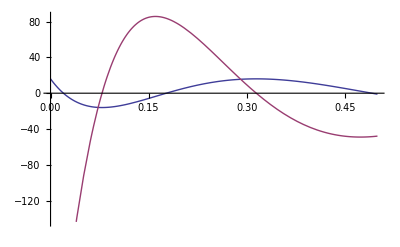

```mathematica
Plot[{psi2p[e1],psi3p[e1]},{e1,0,0.5}]
```

It looks like the boundary condition of the two functions being equal can be met at an energy of about 0.7 eV for the ground state and 0.29 eV for the first excited state. Find the numerical solution to where they are equal for the ground state.

```mathematica
FindRoot[{psi2p[e1]==psi3p[e1]},{e1,0.07}]
```

{e1→0.0727749}

The ground state energy for my problem would be 0.073 eV.

### Your turn

Find the first excited state energy for an electron in a square well of width 0.2 nanometers and with a random height U0 between 10 eV and 20 eV.  I'll get you started by giving you a and the random potential.  Remember to use the correct value for an electron mass and use your potential energy instead of mine.  (Note that U0 will be a different value each time you or someone else evaluates this...)  The first excited state will be the second time ψ_2'(e)=ψ_3'(e), rather than the first time as in my example.

```mathematica
myU0=RandomReal[{10,20}];
mya2 = 0.2;
mymc2 = .511*^6;
myk[e1_]:=Sqrt[2*mymc2*e1/hbarc^2]
myalpha[e1_]:=Sqrt[2*mymc2*(myU0-e1)/hbarc^2]
```

```mathematica
mypsi1[x_,e1_]:=Exp[myalpha[e1]*x]
mypsi2[x_,e1_]:=A*Sin[myk[e1]*x]+B*Cos[myk[e1]*x]
mypsi3[x_, e1_]:=C*Exp[-myalpha[e1]*x]
```

```mathematica
mypsi1prime[x_,e1_]:=Evaluate[D[mypsi1[x,e1],x]]
mypsi2prime[x_,e1_]:=Evaluate[D[mypsi2[x,e1],x]]
mypsi3prime[x_,e1_] := Evaluate[D[mypsi3[x,e1],x]]
```

```mathematica
myeq1=mypsi1[0,e1]==mypsi2[0,e1];
myeq2=mypsi2[a,e1]==mypsi3[a,e1];
myeq3=mypsi1prime[0,e1]==mypsi2prime[0,e1];
myeq4=mypsi2prime[a,e1]==mypsi3prime[a,e1];
```

```mathematica
mysolve = Solve[{myeq2,myeq3,myeq4},{A,B,C}];
```

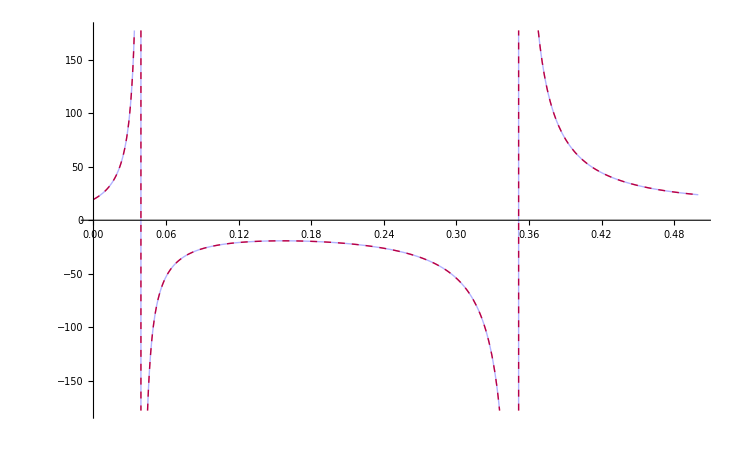

{e1→0.07}

```mathematica
mypsi2p[e1_]:=Evaluate[mypsi2prime[a,e1]/.mysolve[[1]]]
mypsi3p[e1_]:=Evaluate[mypsi3prime[a,e1]/.mysolve[[1]]]
Plot[{mypsi2p[e1],mypsi3p[e1]},{e1,0,0.5},PlotStyle->{{Red,Dashed},{Blue,Thick,Opacity->0.3}}]
FindRoot[{mypsi2p[e1]==mypsi3p[e1]},{e1,0.07}]
```

## Problem 2

A more complicated square well is one where the potential energy isn’t constant.  As an example, let’s consider an infinite square well with a linear slope instead of a constant potential.  We will choose a condition where the walls of the well are at the positions x=0 and x=1.  The potential energy between the walls is 100 x.  Let’s use an electron as our example.  The Schrödinger equation is ψ''(x)==(2 m (100 x-e) ψ(x))/ℏ^2, where e is the energy of the particle.  We’ll use constants in units of eV and an electron.

```mathematica
ClearAll["Global`*"]
m=0.511*^6
ℏc=197
```

We’ll ask Mathematica to solve the Schrödinger Equation subject to the condition that ψ(0)=0.  Then we’ll vary the energy until we find energies for which the absolute value of the wave function is zero at the other wall at x=1.  We use the absolute value of the wave function because it is complex and we need to force both the real and imaginary parts of the wave function to be zero at the boundary.

```mathematica
eq1=psi''[x]==2*m(10x-e) psi[x]/ℏc^2
eq2=psi[0]==0
sol=DSolve[{eq1,eq2},psi[x],x]
```

The solution is in terms of the Airy functions.  They are expressed as a list of Mathematica replacement rules and have an arbitrary constant C[1].  The following code converts this form into a regular function I can plot with the arbitrary constant C[1] set to zero.

```mathematica
psi[x_,e_]:=Evaluate[psi[x]/.sol//First]
psi2[x_,e_]:=psi[x,e]/.C[1]->1
```

The Manipulate function lets me vary the value of e in the graph of the absolute value of the wave function until I can find the places where it goes to 0 at x=1.

```mathematica
Manipulate[Plot[Abs[psi2[x,e]],{x,0,1}, PlotRange->{{0,1},{0,4}}],{e,0,10}]
```

When I slid the slider back and forth, I found approximate values of e at 3.8, 6.2, and 9.4. (Click on the + button at the end of the slider to display the values of the variable.)  The FindRoot function will locate the zeros more precisely once we have an approximate value.  We’ll request just four digits of precision, since that’s all we need.

```mathematica
FindRoot[Abs[psi2[1,e]],{e,3.8},PrecisionGoal->4]
FindRoot[Abs[psi2[1,e]],{e,6.2}, PrecisionGoal->4]
FindRoot[Abs[psi2[1,e]],{e,9.4}, PrecisionGoal->4]
```

Repeat the above exercise with a potentlal U x=10 x^2.  What are the three lowest energies?

## Problem 3

We learned previously that we can estimate the uncertainty of a particle's position as the root mean square width of its probability density.  In the harmonic oscillator, the probability densities for the stationary states are all symmetric about the origin.  This means that the expectation value for x is 0.  In this case, the width of the state is the square root of the expectation value for x^2.  Using the wave functions for the harmonic oscillator given in Table 7.1 of your textbook, find the position uncertainty in nanometers of a particle in the ground state and first two excited states for an electron in a harmonic oscillator with a ground state energy in eV given by random number below. (Be sure to reavaluate it to get your own number instead of mine.)

HINT:  The wave functions in Table 7.1 are unnormalized.  Be sure to normalize them become computing <x^2>.

Here are the wavefunnctions from Table 7.1.
ψ_0(x)=A_0 exp(-x^2/(2 b^2))
ψ_1(x)=(A_1 x exp(-x^2/(2 b^2)))/b
ψ_2(x)=A_2 (1-2 (x/b)^2) exp(-x^2/(2 b^2))

### Example

Let's find the width of a particle with the unnormalized wave function.

```mathematica
psiUnnorm[x_]:=Exp[-3*Abs[x]]
```

First we'll normalize it.

```mathematica
norm=1/Sqrt[Integrate[psiUnnorm[x]^2,{x,-Infinity,Infinity}]]
```

create the normalized wave function

```mathematica
psi[x_]:=norm*psiUnnorm[x]
```

Let' s check and make sure we got it right.

```mathematica
Integrate[psi[x]^2,{x,-Infinity,Infinity}]
```

Since this is a symmetric function with a mean of 0, the width will be

```mathematica
Sqrt[Integrate[psi[x]^2*x^2,{x,-Infinity,Infinity}]]
```

### Your Problem

Here is the energy I want you to use.

```mathematica
E0=1+Random[]
```